### TASK: Which distribution?

Together with this notebook there is a package file Project2.m with a random number generator from secret distributions. Put the package file in the same directory as this notebook. You load the package (once a session) with the following code:

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

You can then use the method randomNumber[i, n] to generate n random numbers from distribution i. For example,

```mathematica
?randomNumber
```

```mathematica
randomNumber[3,10]
```

{19.8728,15.4761,18.4229,20.4069,12.4464,15.0499,14.23,10.9703,8.98031,11.0852}

In this task, randomNumber[i, n] can be used to generate data for the distributions i=1,2,…,6. They are all distributions that are mentioned in the course literature (Blom Sec. 3.4 and Sec. 3.6). Do the following assignments for each of six distributions, i.e. i∈{1,2,…,6}.

Use the straight line approach to determine a distribution model.

Determine point estimates of the parameters.

Compute 95% confidence intervals for the parameters. The interval should not be longer than 10% of its mean, e.g. μ (1±0.05).

1.1 Use the straight line approach to determine a distribution model.

```mathematica
(* declare and generate the 6 unknown distributions *)
(* sort and plot the n points of the distributions *)
n=100;
𝕩1=randomNumber[1,n];
𝕩2=randomNumber[2,n];
𝕩3=randomNumber[3,n];
𝕩4=randomNumber[4,n];
𝕩5=randomNumber[5,n];
𝕩6=randomNumber[6,n];

𝕩1sort=Sort[𝕩1];
𝕩2sort=Sort[𝕩2];
𝕩3sort=Sort[𝕩3];
𝕩4sort=Sort[𝕩4];
𝕩5sort=Sort[𝕩5];
𝕩6sort=Sort[𝕩6];
```

```mathematica
(* facit *)
(*
FindDistribution[𝕩1];
FindDistribution[𝕩2];
FindDistribution[𝕩3];
FindDistribution[𝕩4];
FindDistribution[𝕩5];
FindDistribution[𝕩6];

𝕩1 : ExponentialDistribution[4.52875]
𝕩2 : GeometricDistribution[0.06462]
𝕩3 : GammaDistribution[7.09714,1.80106]
𝕩4 : NormalDistribution[3.00109,5.21337]
𝕩5 : BinomialDistribution[11,0.30072]
𝕩6 : PoissonDistribution[9.881]
*)
```

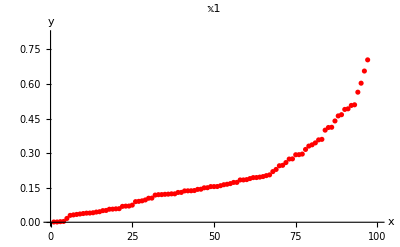

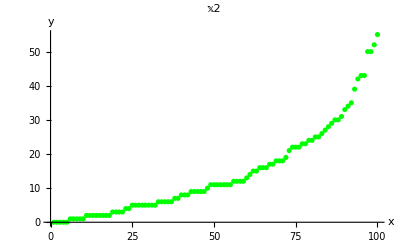

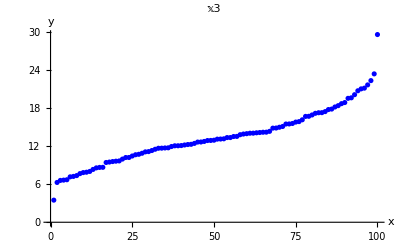

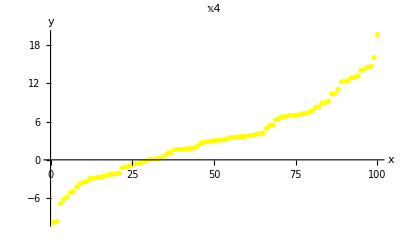

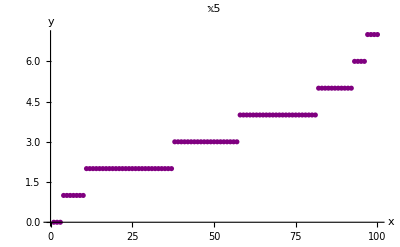

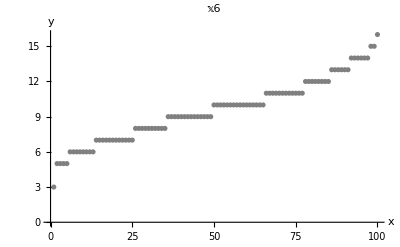

```mathematica
ListPlot[𝕩1sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Red,PlotLabel->"𝕩1"]
ListPlot[𝕩2sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Green,PlotLabel->"𝕩2"]
ListPlot[𝕩3sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Blue,PlotLabel->"𝕩3"]
ListPlot[𝕩4sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Yellow,PlotLabel->"𝕩4"]
ListPlot[𝕩5sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Purple,PlotLabel->"𝕩5"]
ListPlot[𝕩6sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Gray,PlotLabel->"𝕩6"]

(* Below: Plot all the unknown functions in sorted form *)
```

```mathematica
(* 
Let each value correspond to and increase of Δ=1/n probability. Also let each value correspond to the mid point in the Δinterval so the first value Subscript[x, 1] corresponds to P(X≤Subscript[x, 1])=Δ/2 and the value Subscript[x, k] to P(X≤Subscript[x, k])=Δ/2+(k-1) Δ. 
*)
```

```mathematica
Δ=1/n;
𝕡data=Δ/2+Range[0,1-Δ,Δ]//N;
```

```mathematica
(* lineplot to be used to compare the data to the model, declared "globally" here *)
lineplot=Plot[x,{x,0,1}];
```

```mathematica
𝕩1𝕡data=Transpose[{𝕩1sort,𝕡data}];
𝕩2𝕡data=Transpose[{𝕩2sort,𝕡data}];
𝕩3𝕡data=Transpose[{𝕩3sort,𝕡data}];
𝕩4𝕡data=Transpose[{𝕩4sort,𝕡data}];
𝕩5𝕡data=Transpose[{𝕩5sort,𝕡data}];
𝕩6𝕡data=Transpose[{𝕩6sort,𝕡data}];
```

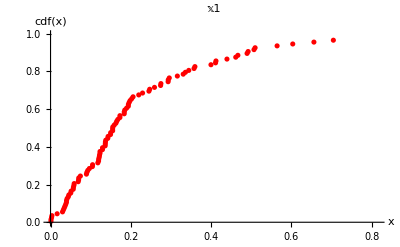

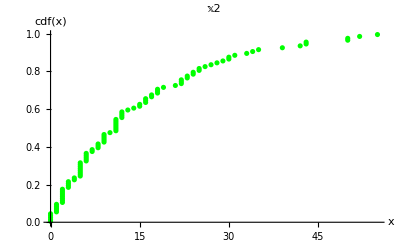

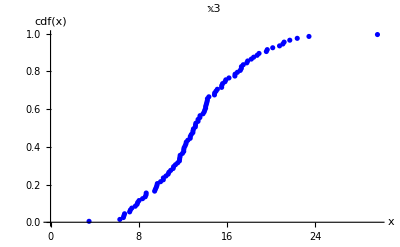

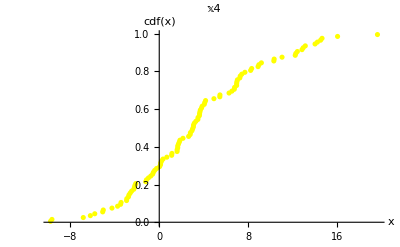

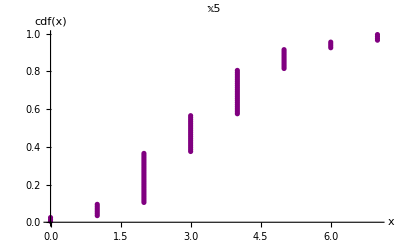

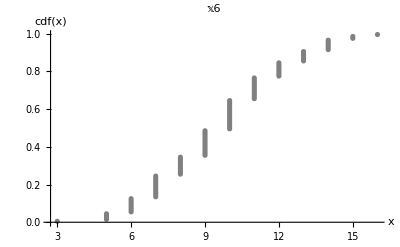

```mathematica
ListPlot[𝕩1𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Red,PlotLabel->"𝕩1"]
ListPlot[𝕩2𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Green,PlotLabel->"𝕩2"]
ListPlot[𝕩3𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Blue,PlotLabel->"𝕩3"]
ListPlot[𝕩4𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Yellow,PlotLabel->"𝕩4"]
ListPlot[𝕩5𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Purple,PlotLabel->"𝕩5"]
ListPlot[𝕩6𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Gray,PlotLabel->"𝕩6"]
```

From the plots it can be concluded that the unknown distributions 𝕩2, 𝕩5 and  𝕩6 are discrete. Distributions 𝕩1,  𝕩3 and 𝕩4 are continuous. The discrete and and continuous cases will be studied separately.

## Discrete distributions [𝕩2, 𝕩5, 𝕩6]

### Distribution 𝕩2

### Distribution 𝕩5

### Distribution 𝕩6

## Continuous distributions [𝕩1, 𝕩3, 𝕩4]

### Distribution 𝕩1

```mathematica
(* 𝕩1 : Normal distribution model-data setup *)
x1=Mean[𝕩1];
s1=StandardDeviation[𝕩1];
𝒩1=NormalDistribution[x1,s1];
𝕡modelNormalDistr𝕩1=CDF[𝒩1,𝕩1sort];
comparedataNormalDistr𝕩1=Transpose[{𝕡modelNormalDistr𝕩1,𝕡data}];
dataplotNormalDistr𝕩1=ListPlot[comparedataNormalDistr𝕩1,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing with Normal Distribution",AspectRatio->Automatic];
Show[dataplotNormalDistr𝕩1,lineplot];
```

```mathematica
(* 𝕩1 : Gamma distribution model-data setup *)
𝒢GammaDistr𝕩1=EstimatedDistribution[𝕩1,GammaDistribution[α,β]];
𝕡modelGammaDistr𝕩1=CDF[𝒢GammaDistr𝕩1,𝕩1sort];
comparedataGammaDistr𝕩1=Transpose[{𝕡modelGammaDistr𝕩1,𝕡data}];
dataplotGammaDistr𝕩1=ListPlot[comparedataGammaDistr𝕩1,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing with Gamma Distribution",AspectRatio->Automatic];
Show[dataplotGammaDistr𝕩1,lineplot];
```

```mathematica
(* 𝕩1 : Weibull distribution model-data setup *)
(* TBD *)
```

```mathematica
(* 𝕩1 : Exponential distribution model-data setup *)
(* TBD *)
```

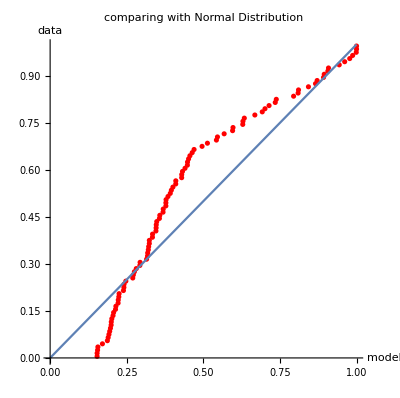

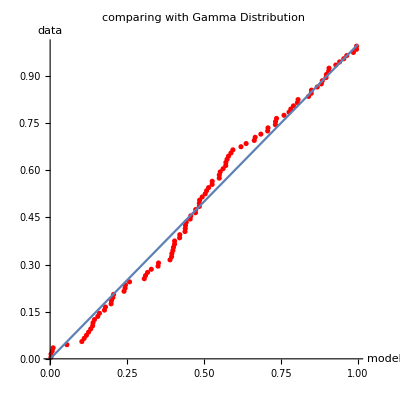

```mathematica
(* Compare the distributiondata to the model from distribution 𝕩1*)
Show[dataplotNormalDistr𝕩1, lineplot]
Show[dataplotGammaDistr𝕩1, lineplot]
```

### Distribution 𝕩3

```mathematica
(* 𝕩3 : Normal distribution model-data setup *)
x3=Mean[𝕩3];
s3=StandardDeviation[𝕩3];
𝒩3=NormalDistribution[x3,s3];
𝕡modelNormalDistr𝕩3=CDF[𝒩3,𝕩3sort];
comparedataNormalDistr𝕩3=Transpose[{𝕡modelNormalDistr𝕩3,𝕡data}];
dataplotNormalDistr𝕩3=ListPlot[comparedataNormalDistr𝕩3,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing with Normal Distribution",AspectRatio->Automatic];
Show[dataplotNormalDistr𝕩3,lineplot];
```

```mathematica
(* 𝕩3 : Gamma distribution model-data setup *)
𝒢GammaDistr𝕩3=EstimatedDistribution[𝕩3,GammaDistribution[α,β]];
𝕡modelGammaDistr𝕩3=CDF[𝒢GammaDistr𝕩3,𝕩3sort];
comparedataGammaDistr𝕩3=Transpose[{𝕡modelGammaDistr𝕩3,𝕡data}];
dataplotGammaDistr𝕩3=ListPlot[comparedataGammaDistr𝕩3,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing with Gamma Distribution",AspectRatio->Automatic];
Show[dataplotGammaDistr𝕩3,lineplot];
```

```mathematica
(* 𝕩3 : Weibull distribution model-data setup *)
(* TBD *)
```

```mathematica
(* 𝕩3 : Exponential distribution model-data setup *)
(* TBD *)
```

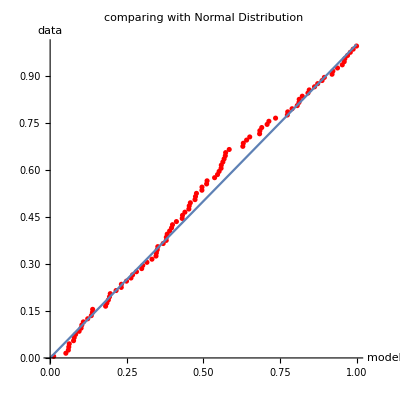

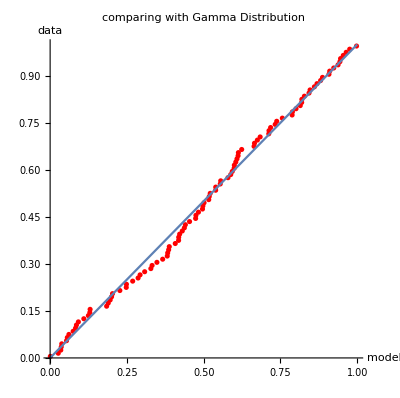

```mathematica
(* Compare the distributiondata to the model from distribution 𝕩3 *)
Show[dataplotNormalDistr𝕩3,lineplot]
Show[dataplotGammaDistr𝕩3,lineplot]
```

### Distribution 𝕩4

```mathematica
(* 𝕩4 : Normal distribution model-data setup *)
x4=Mean[𝕩4];
s4=StandardDeviation[𝕩4];
𝒩4=NormalDistribution[x4,s4];
𝕡modelNormalDistr𝕩4=CDF[𝒩4,𝕩4sort];
comparedataNormalDistr𝕩4=Transpose[{𝕡modelNormalDistr𝕩4,𝕡data}];
dataplotNormalDistr𝕩4=ListPlot[comparedataNormalDistr𝕩4,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing with Normal Distribution",AspectRatio->Automatic];
Show[dataplotNormalDistr𝕩4,lineplot];
```

```mathematica
(* 𝕩4 : Gamma distribution model-data setup *)
(* Gamma distribution is not working (are negative values the cause?) *)
(* 
𝒢GammaDistr𝕩4=EstimatedDistribution[𝕩4,GammaDistribution[α,β]];
𝕡modelGammaDistr𝕩4=CDF[𝒢GammaDistr𝕩4,𝕩4sort];
comparedataGammaDistr𝕩4=Transpose[{𝕡modelGammaDistr𝕩4,𝕡data}];
dataplotGammaDistr𝕩4=ListPlot[comparedataGammaDistr𝕩4,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing with Gamma Distribution",AspectRatio->Automatic];
Show[dataplotGammaDistr𝕩4,lineplot]; 
*)
```

```mathematica
(* 𝕩4 : Weibull distribution model-data setup *)
(* TBD *)
```

```mathematica
(* 𝕩4 : Exponential distribution model-data setup *)
(* TBD *)
```

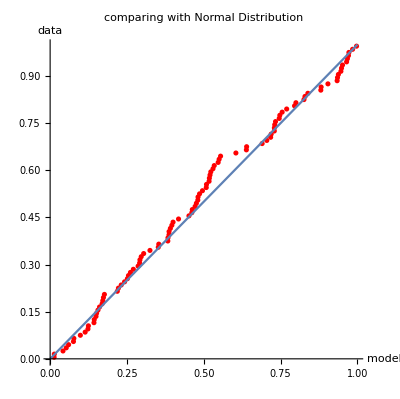

```mathematica
(* Compare the distributiondata to the model from distribution 𝕩4 *)
Show[dataplotNormalDistr𝕩4,lineplot]
```

1.2 Determine point estimates of the parameters.
1.3 Compute 95% confidence intervals for the parameters. The interval should not be longer than 10% of its mean, e.g. μ (1±0.05).

```mathematica
(* Import library *)
Needs["HypothesisTesting`"]
```

### Distribution 𝕩3

```mathematica
(* confidence interval for μ *)
MeanCI[𝕩3, ConfidenceLevel->0.95]

(* confidence interval for σ^2 *)
VarianceCI[𝕩3,ConfidenceLevel->0.95]

(* confidence interval for σ *)
√VarianceCI[𝕩3,ConfidenceLevel->0.95]
```

{12.5604,14.2967}

{14.7568,25.8325}

{3.84146,5.08256}

```mathematica
Clear[α,β];m=100;
𝒟=EstimatedDistribution[𝕩3,GammaDistribution[α,β]]
List@@𝒟
```

GammaDistribution[9.26126,1.44997]

{9.26126,1.44997}

```mathematica
FindDistributionParameters[𝕩3,GammaDistribution[α,β]]
```

{α→9.26126,β→1.44997}

```mathematica
(* repeat enough times so that the CLT gives us good confidence intervals *)
```

```mathematica
𝕩3List={};
randomNumber[3,100];
```

```mathematica
For[i=0,i<50,i++,AppendTo[𝕩3List, {randomNumber[3,100]}]]
```

```mathematica
𝕩3List=Flatten[𝕩3List,1];
```

```mathematica
findαβ[data_]:=List@@EstimatedDistribution[data,GammaDistribution[α,β]]
```

```mathematica
{𝕒,𝕓}=Transpose[findαβ/@𝕩3List]
```

{{9.25336,6.40233,7.18477,9.59519,9.43793,6.56083,7.59098,7.6942,8.26697,7.59618,6.8213,8.2741,11.116,10.6823,8.43811,6.82028,10.0212,8.96365,5.77238,8.82816,7.27967,8.24058,6.77874,9.48908,8.58936,9.5347,9.86095,7.98511,8.81137,6.39524,10.903,8.17975,8.98025,9.06504,6.8539,6.90698,11.1487,8.30115,10.9921,7.98037,6.38319,8.76325,5.7648,9.93951,8.61512,9.92675,7.69599,7.90348,8.0802,9.46405},{1.37004,1.96069,1.73015,1.36854,1.31499,1.85339,1.76194,1.68842,1.56013,1.7856,1.97727,1.54057,1.12342,1.21406,1.59141,1.96875,1.32788,1.50372,2.21197,1.42805,1.62432,1.47895,1.824,1.28232,1.37991,1.4316,1.35991,1.54228,1.4627,1.93357,1.09092,1.60865,1.39535,1.35275,1.87556,1.78059,1.15138,1.53333,1.21524,1.68995,1.96542,1.43886,2.23592,1.24398,1.41027,1.27321,1.61307,1.59722,1.67255,1.41814}}

```mathematica
ciα=MeanCI[𝕒, ConfidenceLevel->0.95]
```

{7.99976,8.80555}

```mathematica
ciαlen=ciα[[2]]-ciα[[1]]
```

0.805789

```mathematica
ciαMid=ciαlen/2
```

0.402895

```mathematica
ciαLeft=ciαMid-(ciαMid*0.05)
ciαRight=ciαMid+(ciαMid*0.05)
```

0.38275

0.423039

```mathematica
ciαMid2=(ciα[[1]]+ciα[[2]])/2
```

8.40265

```mathematica
ciαlenLen2=ciαRight-ciαLeft
```

0.0402895

```mathematica
ciαLLimit=ciαMid2-(ciαlenLen2/2)
```

8.38251

```mathematica
ciαRLimit=ciαMid2+(ciαlenLen2/2)
```

8.4228

```mathematica
ciαInterval={ciαLLimit,ciαRLimit}
```

{8.38251,8.4228}

```mathematica
ciβ=MeanCI[𝕓, ConfidenceLevel->0.95]
```

{1.48531,1.6412}

```mathematica
ciαlen=ciα[[2]]-ciα[[1]]
```

0.805789